```mathematica
(*Plot comp. LS from different conformations and compare to exp lineshape; overlap coefficients*)

(*Import data*)
SetDirectory["/Users/Sherina/Desktop/holo.cam-c-lineshape-no_dihedral"];

l105cExpLSRaw=Import["holo.cam-l105c-exp.dat"];
l105cC1LS=Import["holo.cam-l105c-c.1-0_6ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
l105cC2LS=Import["holo.cam-l105c-c.2-8_10ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
l105cC4LS=Import["holo.cam-l105c-c.4-4_12ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
l105cC5LS=Import["holo.cam-l105c-c.5-0_9ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
l105cC6LS=Import["holo.cam-l105c-c.6-0_1ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
```

```mathematica
m109cExpLSRaw=Import["holo.cam-m109c-exp.dat"];
m109cC2LS=Import["holo.cam-m109c-c.2-2_12ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
m109cC3LS=Import["holo.cam-m109c-c.3-0_10ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
m109cC4LS=Import["holo.cam-m109c-c.4-0_3ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
m109cC5LS=Import["holo.cam-m109c-c.5-2_6ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
m109cC6LS=Import["holo.cam-m109c-c.6-0_4ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
```

```mathematica
m145cExpLSRaw=Import["holo.cam-m145c-exp.dat"];
m145cC2LS=Import["holo.cam-m145c-c.2-4_15ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
m145cC3LS=Import["holo.cam-m145c-c.3-0_15ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
m145cC4LS=Import["holo.cam-m145c-c.4-9_11ns-100fs-12ps-ftir.dat"][[;;,1;;2]];
```

```mathematica
(*In exp. LS: make abs below zero zero*)
l105cExpLS=Table[If[l105cExpLSRaw[[i,2]]≥0,l105cExpLSRaw[[i]],{l105cExpLSRaw[[i,1]],0}],{i,1,Length[l105cExpLSRaw]}];
m109cExpLS=Table[If[m109cExpLSRaw[[i,2]]≥0,m109cExpLSRaw[[i]],{m109cExpLSRaw[[i,1]],0}],{i,1,Length[m109cExpLSRaw]}];
m145cExpLS=Table[If[m145cExpLSRaw[[i,2]]≥0,m145cExpLSRaw[[i]],{m145cExpLSRaw[[i,1]],0}],{i,1,Length[m145cExpLSRaw]}];
```

```mathematica
(*Normalization*)
ListIntegrate[list_,min_,max_]:=(intg=0;For[i=2,i< Length[list],i++, If[list[[i,1]]≥min&&list[[i,1]]≤ max,intg+=list[[i,2]]*(list[[i,1]]-list[[i-1,1]])]];intg)
NormList[list_,min_,max_]:=(intg=ListIntegrate[list,min,max];newlist=Table[{list[[i,1]],list[[i,2]]/intg},{i,1,Length[list]}];newlist)
```

```mathematica
min=2120;(*cm^-1*)
max=2200;(*cm^-1*)

l105cExpLSNorm=NormList[Sort[l105cExpLS],min,max];
l105cC1LSNorm=NormList[l105cC1LS,min,max];
l105cC2LSNorm=NormList[l105cC2LS,min,max];
l105cC4LSNorm=NormList[l105cC4LS,min,max];
l105cC5LSNorm=NormList[l105cC5LS,min,max];
l105cC6LSNorm=NormList[l105cC6LS,min,max];

m109cExpLSNorm=NormList[Sort[m109cExpLS],min,max];
m109cC2LSNorm=NormList[m109cC2LS,min,max];
m109cC3LSNorm=NormList[m109cC3LS,min,max];
m109cC4LSNorm=NormList[m109cC4LS,min,max];
m109cC5LSNorm=NormList[m109cC5LS,min,max];
m109cC6LSNorm=NormList[m109cC6LS,min,max];

m145cExpLSNorm=NormList[Sort[m145cExpLS],min,max];
m145cC2LSNorm=NormList[m145cC2LS,min,max];
m145cC3LSNorm=NormList[m145cC3LS,min,max];
m145cC4LSNorm=NormList[m145cC4LS,min,max];
```

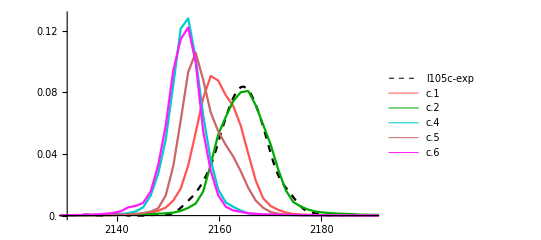

```mathematica
(*Plot*)
ListPlot[{l105cExpLSNorm,l105cC1LSNorm,l105cC2LSNorm,l105cC4LSNorm,l105cC5LSNorm,l105cC6LSNorm},PlotRange->{{2130,2190},All},Joined->True,PlotStyle-> {{Black,Thickness[0.004],Dashed},{Lighter[Red],Thickness[0.004]},{Darker[Green],Thickness[0.004]},{Darker[Cyan,0.2],Thickness[0.004]},{Darker[Pink,0.2],Thickness[0.004]},{Lighter[Magenta,0.1],Thickness[0.004]}},PlotLegends->{"l105c-exp","c.1","c.2","c.4","c.5","c.6"},Ticks->{Table[i,{i,2120,2200,10}],Table[j,{j,0,0.16,0.02}]},TicksStyle-> Black,AxesStyle->Directive[Black,Thickness[0.005],FontSize-> 14],AspectRatio->0.6]
```

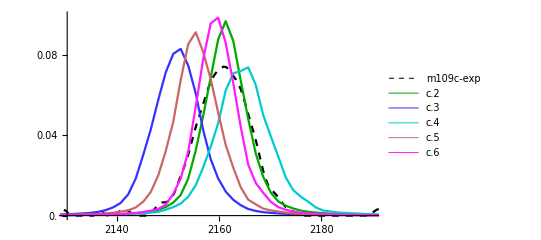

```mathematica
ListPlot[{m109cExpLSNorm,m109cC2LSNorm,m109cC3LSNorm,m109cC4LSNorm,m109cC5LSNorm,m109cC6LSNorm},PlotRange->{{2130,2190},All},Joined->True,PlotStyle-> {{Black,Thickness[0.004],Dashed},{Darker[Green],Thickness[0.004]},{Lighter[Blue,0.2],Thickness[0.004]},{Darker[Cyan,0.2],Thickness[0.004]},{Darker[Pink,0.2],Thickness[0.004]},{Lighter[Magenta,0.1],Thickness[0.004]}},PlotLegends->{"m109c-exp","c.2","c.3","c.4","c.5","c.6"},Ticks->{Table[i,{i,2120,2200,10}],Table[j,{j,0,0.12,0.02}]},TicksStyle-> Black,AxesStyle->Directive[Black,Thickness[0.005],FontSize-> 14],AspectRatio->0.6]
```

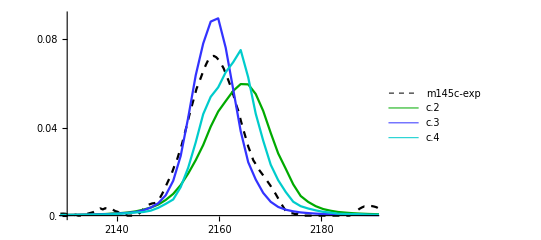

```mathematica
ListPlot[{m145cExpLSNorm,m145cC2LSNorm,m145cC3LSNorm,m145cC4LSNorm},PlotRange->{{2130,2190},All},Joined->True,PlotStyle-> {{Black,Thickness[0.004],Dashed},{Darker[Green],Thickness[0.004]},{Lighter[Blue,0.2],Thickness[0.004]},{Darker[Cyan,0.2],Thickness[0.004]}},PlotLegends->{"m145c-exp","c.2","c.3","c.4"},Ticks->{Table[i,{i,2120,2200,10}],Table[j,{j,0,0.12,0.02}]},TicksStyle-> Black,AxesStyle->Directive[Black,Thickness[0.005],FontSize-> 14],AspectRatio->0.6]
```

```mathematica
(*Overlap coefficients (using list interpolation)*)
(*Overlap coefficients = area under both (normalized)curves*)
l105cExpItp=Interpolation[l105cExpLSNorm];
l105cC1Itp=Interpolation[l105cC1LSNorm];
l105cC2Itp=Interpolation[l105cC2LSNorm];
l105cC4Itp=Interpolation[l105cC4LSNorm];
l105cC5Itp=Interpolation[l105cC5LSNorm];
l105cC6Itp=Interpolation[l105cC6LSNorm];

m109cExpItp=Interpolation[m109cExpLSNorm];
m109cC2Itp=Interpolation[m109cC2LSNorm];
m109cC3Itp=Interpolation[m109cC3LSNorm];
m109cC4Itp=Interpolation[m109cC4LSNorm];
m109cC5Itp=Interpolation[m109cC5LSNorm];
m109cC6Itp=Interpolation[m109cC6LSNorm];

m145cExpItp=Interpolation[m145cExpLSNorm];
m145cC2Itp=Interpolation[m145cC2LSNorm];
m145cC3Itp=Interpolation[m145cC3LSNorm];
m145cC4Itp=Interpolation[m145cC4LSNorm];
```

```mathematica
OverlapCoefficient[f1_[x__],f2_[x__],min_,max_]:=NIntegrate[Min[{f1[x],f2[x]}],{x,min,max}]/(NIntegrate[f1[x],{x,min,max}]*NIntegrate[f2[x],{x,min,max}])
```

```mathematica
min=2120;
max=2200;

TableForm[{{OverlapCoefficient[l105cExpItp[x],l105cC1Itp[x],min,max],OverlapCoefficient[l105cExpItp[x],l105cC2Itp[x],min,max],"N/A",OverlapCoefficient[l105cExpItp[x],l105cC4Itp[x],min,max],OverlapCoefficient[l105cExpItp[x],l105cC5Itp[x],min,max],OverlapCoefficient[l105cExpItp[x],l105cC6Itp[x],min,max]},{"N/A",OverlapCoefficient[m109cExpItp[x],m109cC2Itp[x],min,max],OverlapCoefficient[m109cExpItp[x],m109cC3Itp[x],min,max],OverlapCoefficient[m109cExpItp[x],m109cC4Itp[x],min,max],OverlapCoefficient[m109cExpItp[x],m109cC5Itp[x],min,max],OverlapCoefficient[m109cExpItp[x],m109cC6Itp[x],min,max]},
{"N/A",OverlapCoefficient[m145cExpItp[x],m145cC2Itp[x],min,max],OverlapCoefficient[m145cExpItp[x],m145cC3Itp[x],min,max],OverlapCoefficient[m145cExpItp[x],m145cC4Itp[x],min,max],"N/A","N/A"}},TableHeadings->{{"l105c","m109c","m145c"},{"n.1","n.2","n.3","n.4","n.5","n.6"}}]
```

| n.1 | n.2 | n.3 | n.4 | n.5 | n.6
l105c | 0.614491 | 0.948877 | N/A | 0.189011 | 0.423931 | 0.172478
m109c | N/A | 0.879903 | 0.372382 | 0.710145 | 0.57894 | 0.829953
m145c | N/A | 0.681108 | 0.882233 | 0.754091 | N/A | N/A